```mathematica
(* everything is in AES *)
c1=10;
c2=20;
tax=3.6/100;
diameters={0.5,0.75,1};
cost={19.96,33.5,58.9};
realcost={20.68,34.7,61.02} (*including tax *)
efficiency={41,51,58};
efficiency/realcost(*percent effieciency per dollar*)
```

{20.68,34.7,61.02}

{1.98259,1.46974,0.950508}

```mathematica
(* the most cost-effective solution is the 1/2" diameter pipe*)
```

{{0.5,41},{0.75,51},{1,58}}

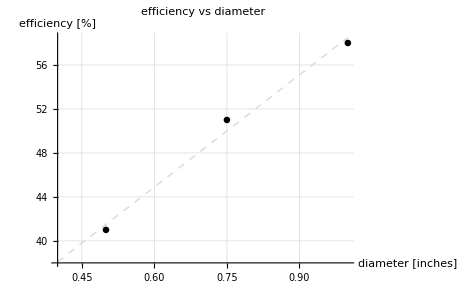

```mathematica
data=Thread[{diameters,efficiency}]
line=Fit[data,{40,x},x];
ideal=Plot[line,{x,0.4,1},PlotStyle->{Dashed,LightGray,Thick}];
meas=ListPlot[data,GridLines->Automatic,PlotStyle->{Black,PointSize[0.01]}];
Show[ideal,meas,GridLines->Automatic,GridLinesStyle->LightGray,PlotLabel->"efficiency vs diameter",AxesLabel->{"diameter [inches]","efficiency [%]"}]
```

#### 1/2” conductor diameter

Antenna efficiency : 41 % (-3.8 dB below 100 %)
Antenna bandwidth : 12.6 kHz
Tuning Capacitance : 114 pF

Capacitor voltage : 742 volts RMS
Resonant circulating current : 3.73 A
Radiation resistance : 0.074 ohms
Loss Resistance : 0.105 ohms
Inductance : 4.52 microhenrys
Inductive Reactance : 199 ohms
Quality Factor (Q) : 554
Distributed capacity : 16 pF

#### 3/4” conductor diameter

Antenna efficiency : 51 % (-2.9 dB below 100 %)
Antenna bandwidth : 9.16 kHz
Tuning Capacitance : 103 pF

Capacitor voltage : 917 volts RMS
Resonant circulating current : 4.16 A
Radiation resistance : 0.074 ohms
Loss Resistance : 0.070 ohms
Inductance : 5.01 microhenrys
Inductive Reactance : 220 ohms
Quality Factor (Q) : 764

#### 1” conductor diameter

Antenna efficiency: 58% (-2.3 dB below 100%)
Antenna bandwidth: 7.52 kHz
Tuning Capacitance: 96 pF

Capacitor voltage: 1,047 volts RMS
Resonant circulating current: 4.44 A
Radiation resistance: 0.074 ohms
Loss Resistance: 0.053 ohms
Inductance: 5.36 microhenrys
Inductive Reactance: 236 ohms
Quality Factor (Q): 931